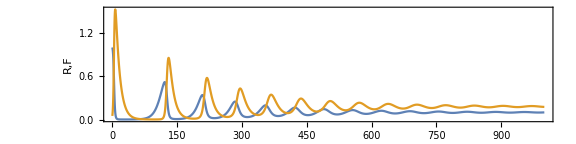

```mathematica
MetapopDyn[a_,λ_,b_,μ_,T_] :=

NDSolve[{
R'[t] ==a*R[t]*(1-R[t]) -(b* Y[t])*R[t] ,
Y'[t] ==λ*Y[t]*R[t]-μ*Y[t],
R[0]==1,Y[0]==0.05},{R,Y},{t,0,T},MaxSteps->Infinity,InterpolationOrder->All];

With[{a=0.1,λ=1,μ=0.1,b=0.5,T=1000},
Traj=Evaluate[{R[t],Y[t]}/.MetapopDyn[a,λ,b,μ,T] ];
Plot[Traj,{t,0,T},PlotRange->{0,All},AspectRatio->0.25,Frame->True,FrameLabel->{"Time","R,F"},ImageSize->Large]
]
```

The below code solves for the steady state

```mathematica
Sol =FullSimplify[Solve[{
0 == α*R*(1-R)-R*(b*Y),
0==λ*Y*R-μ*Y},
{R,X,Y}]]
```

Solve::svars: Equations may not give solutions for all "solve" variables.

{{R→0,Y→0},{R→μ/λ,Y→(α (λ-μ))/(b λ)},{R→1,Y→0}}

Define the single internal Fixed Point (and ensure that all variables are positive for positive parameter values)

```mathematica
InternalSol1 = Sol[[2]];
(*InternalSol2 = Sol[[4]];*)
{InternalSol1}/.{α->1,λ->0.3,μ->0.2,b->0.2}
```

{{R→0.666667,Y→1.66667}}

INTERNAL, POSITIVE SOLUTION

```mathematica
IntPosSol = InternalSol1;
```

Define the internal Fixed Point solutions

```mathematica
Rstar = FullSimplify[IntPosSol[[1]][[2]]]
Fstar = FullSimplify[IntPosSol[[2]][[2]]]
```

μ/λ

(α (λ-μ))/(b λ)

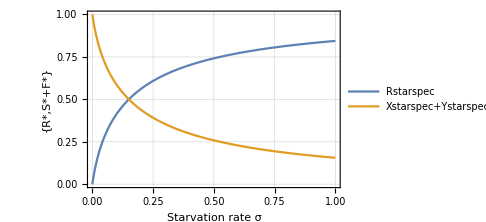
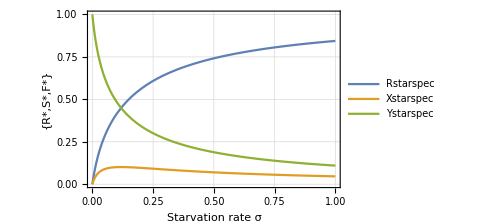

```mathematica
With[{alpha=1,lambda=0.1,mu=0.2,rho=0.2},
Rstarspec = IntPosSol[[1]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Xstarspec = IntPosSol[[2]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Ystarspec = IntPosSol[[3]][[2]]/.{α->alpha,λ->lambda,μ->mu,ρ->rho};
Plot[{Rstarspec,Xstarspec,Ystarspec},{σ,0,1},PlotTheme->"Detailed",FrameLabel->{"Starvation rate σ","{R*,S*,F*}"},PlotRange->{{0,1},{0,1}},ImageSize->Medium]
Plot[{Rstarspec,Xstarspec+Ystarspec},{σ,0,1},PlotTheme->"Detailed",FrameLabel->{"Starvation rate σ","{R*,S*+F*}"},PlotRange->{0,All},ImageSize->Medium]
]
```

```mathematica
dR=   α*R*(1-R)-R*(b*F);
dF =λ*R*F-μ*F;
JacSpec = {
{D[dR,R],D[dR,F]},
{D[dF,R],D[dF,F]}
}
```

{{-b F+(1-R) α-R α,-b R},{F λ,R λ-μ}}

```mathematica
JacSpec//MatrixForm
```

(-b F+(1-R) α-R α | -b R
F λ | R λ-μ)

```mathematica
JacSpecSol = JacSpec/.{R->Rstar,F->Fstar};
```

```mathematica
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,λ]
SaddleBifAnalytic = Solve[Det[JacSpecSol]==0,α]
```

{{λ→μ}}

{{α→0}}

```mathematica
SylvesterMatrix=Function[{Jac},
Dim = Length[Jac];
Mat = Table[0,{Dim-1},{Dim-1}];
Col1 = Table[Subscript[ℼ,i],{i,1,(Dim-1)*2,2}];
Mat[[All,1]] = Col1;
Table[
Mat[[i]][[j]] = Subscript[ℼ,Mat[[i]][[j-1]][[2]]-1];
,{j,2,Dim-1},{i,1,Dim-1,1}];
Todel=Select[Flatten[Mat],#[[2]]<0||#[[2]]>(Dim)&];
Mat=Mat/.Table[Todel[[i]]->0,{i,1,Length[Todel],1}];
CPG = FullSimplify[CharacteristicPolynomial[Jac,λ]];
CPGL = CoefficientList[CPG,λ];
Mat2 = Mat/.Table[Subscript[ℼ,i]-> CPGL[[i+1]],{i,0,(Length[CPGL]-1),1}]
];
```

```mathematica
Sylv=SylvesterMatrix[JacSpecSol];
HopfSol=Solve[Det[Sylv]==0,λ];
```

General::poly: λ^2 + 2\ α\ μ - α\ μ^2/λ is not a polynomial.

```mathematica
Sylv
```

{{0}}

```mathematica
Solve[Tr[JacSpecSol]==0,μ]
```

{{μ→0}}